## Preamble

## Cauchy Riemann Equations

```mathematica
f[z_]:=z^2
ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}
```

x^2+2 ⅈ x y-y^2

```mathematica
Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
```

x^2-y^2

2 x y

```mathematica
D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]

D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]
-D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
```

2 x

2 x

-2 y

-2 y

## Length of a path

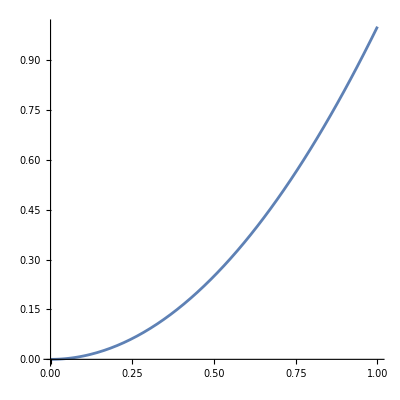

```mathematica
f[x_]:=x^2
Plot[f[x],{x,0,1},AspectRatio->1]
```

```mathematica
f'[t];
f[0];
f[1];
Integrate[√(1+f'[t]^2),{t,0,1}]//N
```

1.47894

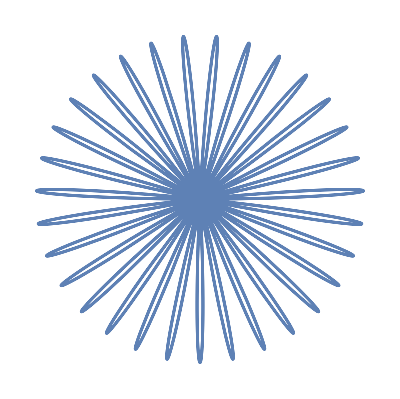

```mathematica
PolarPlot[Sin[31t],{t,0,2Pi},Axes->False]
```